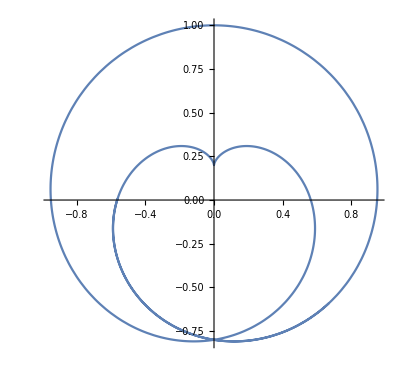

x Cos[π t]-x Cos[2 π t]+(1+y) Sin[π t]-y Sin[2 π t]

π ((1+y) Cos[π t]-2 y Cos[2 π t]-x Sin[π t]+2 x Sin[2 π t])

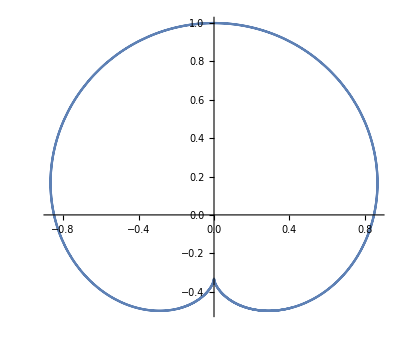

```mathematica
ClearAll["Global`*"]

F[x_,y_,t_,f_,g_]:=Sin[2*Pi*(g[f[t]]-g[t])]-y*(Sin[2*Pi*g[f[t]]]-Sin[2*Pi*g[t]])-x*(Cos[2*Pi*g[f[t]]]-Cos[2*Pi*g[t]]);

Fd[x_,y_,t_,f_,g_]:= 2 Pi( f'[t] g'[f[t]](Cos[2 Pi (g[f[t]]-g[t])]-y Cos[2 Pi g[f[t]]]+x Sin[2 Pi g[f[t]]])-g'[t](Cos[2 Pi (g[f[t]]-g[t])]-y Cos[2 Pi g[t]] +x Sin[2 Pi g[t]]) );

parametricFunc[t_,f_,g_]:={x,y}/.(Solve[F[x,y,t,f,g]==0&&Fd[x,y,t,f,g]==0,{x,y}]);

plot[f_,g_,from_,to_]:=ParametricPlot[parametricFunc[t,f,g],{t,from,to}];
(* Heart *)
a=3;
f1[x_]:=x*a;
g1[x_]:=x/2^Floor[Log[x]];
(*plot[f1, g1, E,E^2-0.698]*)

f2[x_]:=x*a/2;
g2[x_]:=x/2;
plot[f2, g2, E,E^2]

(* Original Cardioid *)
a=4;
f1[x_]:=x*a;
g1[x_]:=x/2^Floor[Log[x]];
(*plot[f1, g1, E,E+2]*)

f2[x_]:=x*a/2;
g2[x_]:=x/2;
Print[FullSimplify[F[x,y,t,f2,g2]]];
Print[FullSimplify[Fd[x,y,t,f2,g2]]];
plot[f2, g2, E,E^2]
```